Helper tools

```mathematica
ClearAll["Global`*"]
basepath="/Users/basavyr/Documents/Work/Repos/mathematica-useful-algorithms/Physics/Elliptic-Functions-New-Boson/Figures/Frequencies";
thesispath="/Users/basavyr/Documents/Work/PhD/phdthesis/Chapters/Figures";
export[object_,name_,format_]:=Export[StringTemplate["``/``.``"][thesispath,name,format],object, ImageResolution->1500];
linspace[a_,b_,n_]:=Table[N[q],{q,a,b,(b-a)/(n-1)}];
```

Numerical values

```mathematica
MOIfit1={91,9,51};
MOIfit2={13.53,101.76,52.94};
MOIfit3={89,12,48};
thetadegfit1=-119;
thetadegfit2=140;
thetadegfit3=-71;
oddspin=5.5;
Ak[mois_]:=N[1/(2*#)]&/@mois;
rad[thetadeg_]:=N[thetadeg*π/180];
j1[thetadeg_]:=oddspin*Cos[rad[thetadeg]];
j2[thetadeg_]:=oddspin*Sin[rad[thetadeg]];
```

Analytical Formulas

```mathematica
A[I_,thetadeg_,mois_]:=Ak[mois][[2]](1-j2[thetadeg]/I)-Ak[mois][[1]];
u[I_,thetadeg_,mois_]:=(Ak[mois][[3]]-Ak[mois][[1]])/A[I,thetadeg,mois];
v0[I_,thetadeg_,mois_]:=-(Ak[mois][[1]]*j1[thetadeg])/A[I,thetadeg,mois];
```

## The wobbling frequency evaluated for 135Pr

Omega ω

```mathematica
A21[I_,thetadeg_,mois_]:=(Ak[mois][[2]]-Ak[mois][[1]]-(Ak[mois][[2]]*j2[thetadeg])/I);
omega[I_,thetadeg_,mois_]:=(((2I+1)*A21[I,thetadeg,mois]+2*Ak[mois][[1]]*j1[thetadeg])*((2I+1)*(Ak[mois][[3]]-Ak[mois][[1]])+2*Ak[mois][[1]]*j1[thetadeg])-(Ak[mois][[3]]-Ak[mois][[1]])*A21[I,thetadeg,mois])^(1/2);
```

Omega ω’

```mathematica
omegaPrime[I_,thetadeg_,mois_]:=(((2I+1)*A21[I,thetadeg,mois]-2*Ak[mois][[1]]*j1[thetadeg])*((2I+1)*(Ak[mois][[3]]-Ak[mois][[1]])-2*Ak[mois][[1]]*j1[thetadeg])-(Ak[mois][[3]]-Ak[mois][[1]])*A21[I,thetadeg,mois])^(1/2);
```

Helper tools for the tabulated values

```mathematica
header1={"I","ω-1","ω_π-1","ω-2","ω_π-2","ω-3","ω_π-3"};
header2={"I","ω'-1","ω'_π-1","ω'-2","ω'_π-2","ω'-3","ω'_π-3"};
spinvalues=Table[spin,{spin,7.5,39.5,2}];
```

Numerical values  for ω(tabulated)

```mathematica
omegavaluesfit1=Table[{omega[spin,thetadegfit1,MOIfit1],omega[spin,thetadegfit1+180,MOIfit1]},{spin,spinvalues}];
omegavaluesfit2=Table[{omega[spin,thetadegfit2,MOIfit2],omega[spin,thetadegfit2+180,MOIfit2]},{spin,spinvalues}];
omegavaluesfit3=Table[{omega[spin,thetadegfit3,MOIfit3],omega[spin,thetadegfit3+180,MOIfit3]},{spin,spinvalues}];
numericalvalues1=Table[{spinvalues[[i]],omegavaluesfit1[[i,1]],omegavaluesfit1[[i,2]],omegavaluesfit2[[i,1]],omegavaluesfit2[[i,2]],omegavaluesfit3[[i,1]],omegavaluesfit3[[i,2]]},{i,1,Length[spinvalues]}];
numericalvalues1=Insert[numericalvalues1,header1,1];
```

Numerical values  for ω’(tabulated)

```mathematica
omegaprimevaluesfit1=Table[{omegaPrime[spin,thetadegfit1,MOIfit1],omegaPrime[spin,thetadegfit1+180,MOIfit1]},{spin,spinvalues}];
omegaprimevaluesfit2=Table[{omegaPrime[spin,thetadegfit2,MOIfit2],omegaPrime[spin,thetadegfit2+180,MOIfit2]},{spin,spinvalues}];
omegaprimevaluesfit3=Table[{omegaPrime[spin,thetadegfit3,MOIfit3],omegaPrime[spin,thetadegfit3+180,MOIfit3]},{spin,spinvalues}];
numericalvalues2=Table[{spinvalues[[i]],omegaprimevaluesfit1[[i,1]],omegaprimevaluesfit1[[i,2]],omegaprimevaluesfit2[[i,1]],omegaprimevaluesfit2[[i,2]],omegaprimevaluesfit3[[i,1]],omegaprimevaluesfit3[[i,2]]},{i,1,Length[spinvalues]}];
numericalvalues2=Insert[numericalvalues2,header2,1];
```

```mathematica
gg1=Grid[numericalvalues1,Frame->All];
gg2=Grid[numericalvalues2,Frame->All];
gg1
gg2
```

I | ω-1 | ω_π-1 | ω-2 | ω_π-2 | ω-3 | ω_π-3
7.5 | 0.229851 | 0.159683 | 0.803892 | 0.142569 | 0.319873 | 0.0729018
9.5 | 0.294886 | 0.232257 | 0.922509 | 0.262878 | 0.37244 | 0.136003
11.5 | 0.357647 | 0.298689 | 1.04118 | 0.382287 | 0.425068 | 0.193021
13.5 | 0.419196 | 0.36242 | 1.15989 | 0.501416 | 0.477717 | 0.248146
15.5 | 0.480018 | 0.424686 | 1.27861 | 0.620417 | 0.530372 | 0.3024
17.5 | 0.540366 | 0.48606 | 1.39734 | 0.739349 | 0.583027 | 0.356175
19.5 | 0.600387 | 0.546848 | 1.51608 | 0.858237 | 0.635679 | 0.409655
21.5 | 0.660174 | 0.607228 | 1.63482 | 0.977096 | 0.688329 | 0.462941
23.5 | 0.719786 | 0.667313 | 1.75357 | 1.09594 | 0.740975 | 0.516092
25.5 | 0.779264 | 0.727176 | 1.87232 | 1.21476 | 0.793618 | 0.569144
27.5 | 0.838637 | 0.78687 | 1.99107 | 1.33357 | 0.846258 | 0.622123
29.5 | 0.897927 | 0.84643 | 2.10982 | 1.45238 | 0.898896 | 0.675045
31.5 | 0.957149 | 0.905883 | 2.22857 | 1.57118 | 0.951531 | 0.727924
33.5 | 1.01632 | 0.965249 | 2.34733 | 1.68997 | 1.00416 | 0.780766
35.5 | 1.07544 | 1.02454 | 2.46608 | 1.80876 | 1.05679 | 0.83358
37.5 | 1.13452 | 1.08378 | 2.58484 | 1.92755 | 1.10942 | 0.88637
39.5 | 1.19357 | 1.14296 | 2.70359 | 2.04633 | 1.16205 | 0.93914

I | ω'-1 | ω'_π-1 | ω'-2 | ω'_π-2 | ω'-3 | ω'_π-3
7.5 | 0.370437 | 0.0890459 | 0.172458 | 0.768548 | 0.239624 | 0.114072
9.5 | 0.42855 | 0.15228 | 0.294059 | 0.887752 | 0.295775 | 0.181697
11.5 | 0.486895 | 0.213141 | 0.413948 | 1.00682 | 0.35077 | 0.241885
13.5 | 0.545367 | 0.273157 | 0.533304 | 1.12582 | 0.405102 | 0.29919
15.5 | 0.603914 | 0.332761 | 0.652428 | 1.24476 | 0.459018 | 0.355024
17.5 | 0.66251 | 0.39213 | 0.771432 | 1.36366 | 0.512653 | 0.409995
19.5 | 0.72114 | 0.451351 | 0.890365 | 1.48254 | 0.566089 | 0.464412
21.5 | 0.779794 | 0.510471 | 1.00925 | 1.6014 | 0.619381 | 0.518451
23.5 | 0.838465 | 0.569521 | 1.12811 | 1.72024 | 0.672562 | 0.572221
25.5 | 0.897149 | 0.628518 | 1.24695 | 1.83908 | 0.725658 | 0.625791
27.5 | 0.955844 | 0.687477 | 1.36578 | 1.9579 | 0.778687 | 0.67921
29.5 | 1.01455 | 0.746404 | 1.48459 | 2.07671 | 0.831661 | 0.732511
31.5 | 1.07326 | 0.805308 | 1.60339 | 2.19552 | 0.884592 | 0.785717
33.5 | 1.13197 | 0.864192 | 1.72219 | 2.31432 | 0.937485 | 0.838848
35.5 | 1.19069 | 0.92306 | 1.84098 | 2.43312 | 0.990348 | 0.891916
37.5 | 1.24941 | 0.981914 | 1.95977 | 2.55191 | 1.04318 | 0.944933
39.5 | 1.30814 | 1.04076 | 2.07855 | 2.6707 | 1.096 | 0.997906

Helper functions for plotting

```mathematica
generalStyle[function_,colors_,thetadeg_]:={PlotLegends->Placed[{StringTemplate["(``)^o"][thetadeg],StringTemplate["(``)^o"][thetadeg+180]},{0.8,0.25}],
PlotMarkers->{{"■", 14}, {"●", 14}},
PlotStyle->{{colors[[1]]},{colors[[2]]}},
ImageSize->350,
LabelStyle->{18,Black,FontFamily->"Latin Modern Roman"},
AspectRatio->0.6,
Frame->True,
Axes->False,
FrameStyle->Directive[Black,Thick],
FrameTicks->{{All,Automatic},{All,Automatic}},
FrameLabel->{"I [ℏ]",function}};
lp[omegavalues_,thetadeg_,function_,colors_,mois_]:=ListLinePlot[{
Table[{spinvalues[[idx]],omegavalues[[idx,1]]},{idx,1,Length[spinvalues]}],
Table[{spinvalues[[idx]],omegavalues[[idx,2]]},{idx,1,Length[spinvalues]}]},
Evaluate[generalStyle[function,colors,thetadeg]],
Epilog->{Inset[Style[StringTemplate["ℐ_1:ℐ_2:ℐ_3=``:``:``"][Round[mois[[1]]],Round[mois[[2]]],Round[mois[[3]]]],19,Black,FontFamily->"Latin Modern Roman"],Scaled[{0.32,0.87}]]}
];
```

Graphical representations for ω

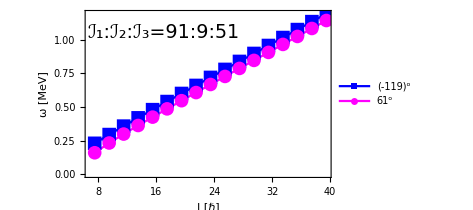

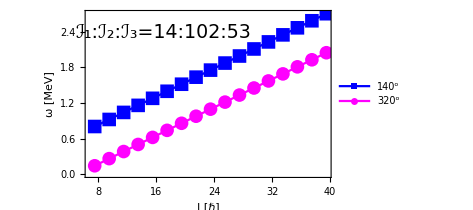

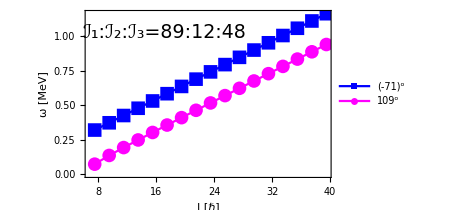

```mathematica
lp1=lp[omegavaluesfit1,thetadegfit1,"ω [MeV]",{Blue,Magenta},MOIfit1];
Show[lp1]
export[lp1,"omega-fit-1","pdf"];
lp2=lp[omegavaluesfit2,thetadegfit2,"ω [MeV]",{Blue,Magenta},MOIfit2];
Show[lp2]
export[lp2,"omega-fit-2","pdf"];
lp3=lp[omegavaluesfit3,thetadegfit3,"ω [MeV]",{Blue,Magenta},MOIfit3];
Show[lp3]
export[lp3,"omega-fit-3","pdf"];
```

Graphical representations for ω’

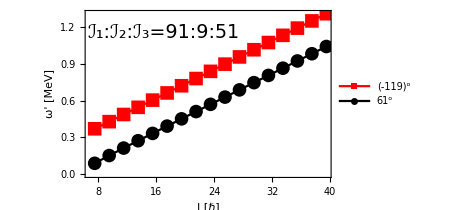

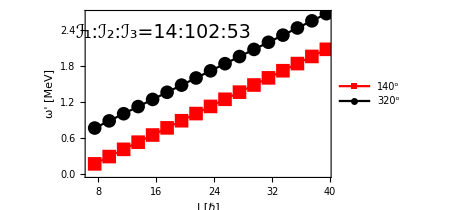

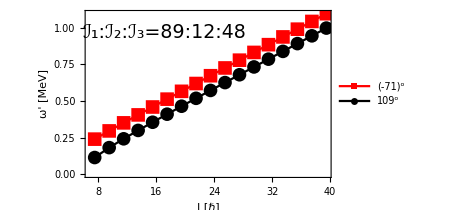

```mathematica
lp1prime=lp[omegaprimevaluesfit1,thetadegfit1,"ω' [MeV]",{Red,Black},MOIfit1];
Show[lp1prime]
export[lp1prime,"omega-prime-fit-1","pdf"];
lp2prime=lp[omegaprimevaluesfit2,thetadegfit2,"ω' [MeV]",{Red,Black},MOIfit2];
Show[lp2prime]
export[lp2prime,"omega-prime-fit-2","pdf"];
lp3prime=lp[omegaprimevaluesfit3,thetadegfit3,"ω' [MeV]",{Red,Black},MOIfit3];
Show[lp3prime]
export[lp3prime,"omega-prime-fit-3","pdf"];
```